```mathematica
Quit[]
```

```mathematica
Get["DdimPackage.wl"]
```

Get::noopen: Cannot open YoungSymm`.

Needs::nocont: Context YoungSymm` was not created when Needs was evaluated.

```mathematica
Get["/Users/gangchen/Documents/GitHub/WaveFormOneLoopQM/Amplitude/1-loop_HEFT_amplitude_result.wl"]
```

parametrise picks a frame (here I am considering the ϵ_k^+ helicity polarisation):

## Plus Polarisation

```mathematica
ClearAll[parametrise]
parametrise[exp_]:=ReplaceRepeated[exp,{DotProduct[Momentum[x_],Momentum[y_]]:>x.DiagonalMatrix[{1,-1,-1,-1}].y,DotProduct[EpsilonPol[k],Momentum[y_]]:>ϵk.DiagonalMatrix[{1,-1,-1,-1}].y}]/.{u1->{1,0,0,0},u2->{γ,V γ,0,0},k->ω{1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},b->{0,0,B,0},v->{0,0,0,4 B √(-1+γ^2)},ϵk->{0,(Cos[θ] Cos[ϕ]-I Sin[ϕ]),(Cos[θ] Sin[ϕ]+I Cos[ϕ]),-Sin[θ]}}
```

```mathematica
(*{k.DiagonalMatrix[{1,-1,-1,-1}].{ϵk0,ϵk1,ϵk2,ϵk3},{ϵk0,ϵk1,ϵk2,ϵk3}.DiagonalMatrix[{1,-1,-1,-1}].{ϵk0,ϵk1,ϵk2,ϵk3}}/.{u1->{1,0,0,0},u2->{γ,γ v,0,0},k->ω{1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},b->{0,0,b,0},v->{0,0,0,4 b Sqrt[γ^2-1]}}
Solve[%==0,{ϵk0,ϵk1}][[1]]
%/.θ->0/.{ϵk3->0,ϵk2->1}*)
```

```mathematica
g0=115/100;
```

```mathematica
amp1=-I amp5TreeLevel/. replaceTree;
```

```mathematica
(*amp5=amp5m13m22/. replaceDivergences/. amp5TreeLevel->0/. replacer[]/. replacelq[]/. replacely[]/. replacelw2[]/.replaceTriangleIntegrals/.replacec1/.replacec2;*)
```

```mathematica
amp1//.{F1->FTrace[Momentum[q1],{FieldStr[k]},Momentum[v1]],F2->FTrace[Momentum[q2],{FieldStr[k]},Momentum[v2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
(*%//Reduce`FreeVariables*)
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->g0(*ω->3*)};
amp1=%+ReplaceAll[%,zv->-zv]//Expand[#,1]&;
(*%//Series[#,zv->Infinity]&
%%//Series[#,{zb,Infinity,0}]&*)
```

```mathematica
amp1//Length
```

2

### Continue

```mathematica
Monitor[amp1=Sum[amp1[[ii]]//Simplify,{ii,Length@amp1}];,ii]
```

```mathematica
amp1//Simplify
```

(129 √129 (-5474889 ⅈ √2 (-129 ⅈ+46 √129) zb^5+33282 (122441+30268 ⅈ √129) zb^4 ω-258 ⅈ √2 zb^3 (42441 (-129 ⅈ+46 √129) zv^2+(-60067689 ⅈ+14824972 √129) ω^2)+258 zb^2 (516 (40000+7567 ⅈ √129) zv^2 ω+529 (545641+48668 ⅈ √129) ω^3)-3 ⅈ √2 zb (1824963 (-129 ⅈ+46 √129) zv^4+86 (-4215333 ⅈ+10920400 √129) zv^2 ω^2+529 (-53201363 ⅈ+5913162 √129) ω^4)+1058 (1181511 zv^4 ω+129 (254359+18400 ⅈ √129) zv^2 ω^3+169280000 ω^5)))/(8464000 ω (129 zb^2+129 zv^2+529 ω^2) (129 zb^2+129 zv^2-129 √2 zb ω-129 √2 zv ω+529 ω^2) (129 zb^2+129 zv^2-129 √2 zb ω+129 √2 zv ω+529 ω^2))

```mathematica
amp1list=List@@(amp1//Apart[#,zb]&//Expand);
```

```mathematica
(List@@@(Denominator/@amp1list))//Flatten//Union
```

{5,10,20,500,1000,2000,2750,30250,√2,ω,21 zb^2+21 zv^2+121 ω^2,42 zv^2+121 ω^2,21 zb^2+21 zv^2-21 √2 zb ω-21 √2 zv ω+121 ω^2,21 zb^2+21 zv^2-21 √2 zb ω+21 √2 zv ω+121 ω^2}

```mathematica
(-zb^2-zv^2+zb^2 γ^2+zv^2 γ^2+√2 zb ω-√2 zv ω-√2 zb γ^2 ω+√2 zv γ^2 ω+γ^2 ω^2)/.zb->zb+(√2)/2 ω//Simplify
```

zb^2 (-1+γ^2)+zv^2 (-1+γ^2)+√2 zv (-1+γ^2) ω+1/2 (1+γ^2) ω^2

```mathematica
amp1list=amp1list/.Times[f__,Power[(258 zb^2+258 zv^2+258 √2 zv ω+929 ω^2),-1]]:>(Exp[I (√2)/2 ω]Times[f,Power[(258 zb^2+258 zv^2+258 √2 zv ω+929 ω^2),-1]]/.zb->zb+(√2)/2 ω//Simplify)/.Times[f__,Power[(129 zb^2+129 zv^2-129 √2 zb ω+129 √2 zv ω+529 ω^2),-1]]:>(Exp[I (√2)/2 ω]Times[f,Power[(129 zb^2+129 zv^2-129 √2 zb ω+129 √2 zv ω+529 ω^2),-1]]/.zb->zb+(√2)/2 ω//Simplify)/.Times[f__,Power[(129 zb^2+129 zv^2-129 √2 zb ω-129 √2 zv ω+529 ω^2),-1]]:>(Exp[I (√2)/2 ω]Times[f,Power[(129 zb^2+129 zv^2-129 √2 zb ω-129 √2 zv ω+529 ω^2),-1]]/.zb->zb+(√2)/2 ω//Simplify);
```

```mathematica
(-zb^2-zv^2+zb^2 γ^2+zv^2 γ^2+√2 zb ω-√2 zv ω-√2 zb γ^2 ω+√2 zv γ^2 ω+γ^2 ω^2)*400/.γ->g0//Expand
```

129 zb^2+129 zv^2-129 √2 zb ω+129 √2 zv ω+529 ω^2

```mathematica
Monitor[amp1list000=Table[Assuming[zv>0&ω>0,Integrate[amp1list[[ii]] Exp[-I zb],{zb,-∞,+∞}]]//PowerExpand,{ii,Length@amp1list}];,ii]
```

```mathematica
Monitor[amp1list0=Table[Assuming[b>0,√(2 π)FourierTransform[amp1list[[ii]],zb,b]]/.b->1/.ω->-ω//PowerExpand,{ii,Length@amp1list}];,ii]
```

```mathematica
Monitor[amp1list00=Table[Assuming[b<0,√(2 π)FourierTransform[amp1list[[ii]],zb,b]]/.b->-1//PowerExpand,{ii,Length@amp1list}];,ii]
```

```mathematica
amp1list[[13]]
```

-(382743 ⅈ ⅇ^((ⅈ ω)/(√2)) zv ω)/(5 √2 (258 zv^2+529 ω^2) (258 zb^2+258 zv^2-258 √2 zv ω+929 ω^2))

```mathematica
amp10PP0=amp1list00//Total;
```

```mathematica
amp10PP=amp1list0//Total;
```

```mathematica
amp10PP00=amp1list000//Total;
```

```mathematica
amp10PP00[[2]]
```

√(-258 zv^2-258 √2 zv ω-929 ω^2)≠0&&((Re[√(-258 zv^2-258 √2 zv ω-929 ω^2)]≤0&&(929 ω^2+258 Re[zv (zv+√2 ω)]>0||zv (zv+√2 ω)∉ℝ))||√(-258 zv^2-258 √2 zv ω-929 ω^2)∉ℝ)&&√(-258 zv^2+258 √2 zv ω-929 ω^2)≠0&&((Re[√(-258 zv^2+258 √2 zv ω-929 ω^2)]≤0&&(929 ω^2+258 Re[zv (zv-√2 ω)]>0||zv (zv-√2 ω)∉ℝ))||√(-258 zv^2+258 √2 zv ω-929 ω^2)∉ℝ)&&Im[√(-129 zv^2-529 ω^2)]>0

```mathematica
NIntegrate[amp10PP/.ω->3.5,{zv,0.01,∞}]
```

-0.000211257+0.000828854 ⅈ

```mathematica
NIntegrate[amp10PP00/.ω->3.5,{zv,0.01,∞}]
```

0.000252447+0.000533383 ⅈ

```mathematica
NIntegrate[amp10PP0/.ω->3.5,{zv,0.01,∞}]
```

0.000252447+0.000533383 ⅈ

```mathematica
amp1Reg=(amp1)* Exp[-I zb-0.0001Abs[zb]];
ampNumUnReg=amp1Reg/.ω->3.5;NIntegrate[ampNumUnReg,{zv,0,∞},{zb,-∞,+∞},Method->"LocalAdaptive"]
```

-0.00020271+0.000836349 ⅈ

```mathematica
{0,(Cos[θ] Cos[ϕ]-I Sin[ϕ]),(Cos[θ] Sin[ϕ]+I Cos[ϕ]),-Sin[θ]}/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->g0(*ω->3*)}
```

{0,-ⅈ,1/(√2),-1/(√2)}

```mathematica
{0,(Cos[θ] Cos[ϕ]+I Sin[ϕ]),(Cos[θ] Sin[ϕ]-I Cos[ϕ]),-Sin[θ]}/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->g0(*ω->3*)}
```

{0,ⅈ,1/(√2),-1/(√2)}

```mathematica
g0
```

23/20

## Minus Polarisation

```mathematica
ClearAll[parametrise]
parametrise[exp_]:=ReplaceRepeated[exp,{DotProduct[Momentum[x_],Momentum[y_]]:>x.DiagonalMatrix[{1,-1,-1,-1}].y,DotProduct[EpsilonPol[k],Momentum[y_]]:>ϵk.DiagonalMatrix[{1,-1,-1,-1}].y}]/.{u1->{1,0,0,0},u2->{γ,V γ,0,0},k->ω{1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},b->{0,0,B,0},v->{0,0,0,4 B √(-1+γ^2)},ϵk->{0,(Cos[θ] Cos[ϕ]+I Sin[ϕ]),(Cos[θ] Sin[ϕ]-I Cos[ϕ]),-Sin[θ]}}
```

```mathematica
(*{k.DiagonalMatrix[{1,-1,-1,-1}].{ϵk0,ϵk1,ϵk2,ϵk3},{ϵk0,ϵk1,ϵk2,ϵk3}.DiagonalMatrix[{1,-1,-1,-1}].{ϵk0,ϵk1,ϵk2,ϵk3}}/.{u1->{1,0,0,0},u2->{γ,γ v,0,0},k->ω{1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},b->{0,0,b,0},v->{0,0,0,4 b Sqrt[γ^2-1]}}
Solve[%==0,{ϵk0,ϵk1}][[1]]
%/.θ->0/.{ϵk3->0,ϵk2->1}*)
```

```mathematica
amp1=-I amp5TreeLevel/. replaceTree;
```

```mathematica
(*amp5=amp5m13m22/. replaceDivergences/. amp5TreeLevel->0/. replacer[]/. replacelq[]/. replacely[]/. replacelw2[]/.replaceTriangleIntegrals/.replacec1/.replacec2;*)
```

```mathematica
amp1//.{F1->FTrace[Momentum[q1],{FieldStr[k]},Momentum[v1]],F2->FTrace[Momentum[q2],{FieldStr[k]},Momentum[v2]],F3->FTrace[Momentum[v1],{FieldStr[k]},Momentum[v2]]};
%//.FTrace[a_,{FieldStr[k_]},b_]:>DotProduct[a,Momentum[k]]DotProduct[b,EpsilonPol[k]]-DotProduct[b,Momentum[k]]DotProduct[a,EpsilonPol[k]];
%//.{qq1->-DotProduct[Momentum[q1],Momentum[q1]],qq2->-DotProduct[Momentum[q2],Momentum[q2]],w1->DotProduct[Momentum[v1],Momentum[k]],w2->DotProduct[Momentum[v2],Momentum[k]],y->DotProduct[Momentum[v1],Momentum[v2]]};
%//.{v2->u2,v1->u1,y->γ};
%/.{Momentum[q2]->Momentum[k]-Momentum[q1]};
Sqrt[(γ^2-1)]%//.{Momentum[q1]->z1 Momentum[u1]+z2 Momentum[u2]+zb Momentum[bt]+zv Momentum[vt]};
%//.{DotProduct[Momentum[u1],Momentum[u2]]->γ,DotProduct[Momentum[bt],Momentum[bt]]->-1,DotProduct[Momentum[vt],Momentum[vt]]->-1,DotProduct[Momentum[u1],Momentum[u1]]->1,DotProduct[Momentum[u2],Momentum[u2]]->1};
%//.{DotProduct[Momentum[u1],Momentum[bt]]->0,DotProduct[Momentum[u2],Momentum[bt]]->0,DotProduct[Momentum[u1],Momentum[vt]]->0,DotProduct[Momentum[u2],Momentum[vt]]->0,DotProduct[Momentum[vt],Momentum[bt]]->0};
%/.{z1->(DotProduct[Momentum[u2],Momentum[k]] γ)/(-1+γ^2),z2->-DotProduct[Momentum[u2],Momentum[k]]/(-1+γ^2)};
%/.{Momentum[bt]->Momentum[b]/Sqrt[-DotProduct[Momentum[b],Momentum[b]]],Momentum[vt]->Momentum[v]/(4Sqrt[-DotProduct[Momentum[b],Momentum[b]](γ^2-1)])}/.γ->DotProduct[Momentum[u1],Momentum[u2]]//parametrise;
%/.{V->(√(-1+γ^2))/γ,B->b};
(*%//Reduce`FreeVariables*)
%/.{ϕ->Pi/2,θ->Pi/4,b->1,γ->g0(*ω->3*)};
amp1=%+ReplaceAll[%,zv->-zv]//Expand[#,1]&;
(*%//Series[#,zv->Infinity]&
%%//Series[#,{zb,Infinity,0}]&*)
```

```mathematica
amp1//Length
```

2

```mathematica
amp1
```

√3 ((√3 (8 ⅈ √3 ω^3-16 ω^2 (-zb/(√2)+zv/(√2)+(2 ⅈ ω)/(√3))-8 ω (-2 ω (zb/(√2)-zv/(√2)-(2 ⅈ ω)/(√3))-ⅈ √3 ((zb ω)/(√2)+(zv ω)/(√2)))-4 ⅈ √3 ω (2 (-(zb ω)/(√2)-(zv ω)/(√2))-2 (-zb^2-zv^2-(4 ω^2)/3))))/(8 ω (-zb^2-zv^2-(4 ω^2)/3) (-zb^2-zv^2-(4 ω^2)/3-2 (-(zb ω)/(√2)-(zv ω)/(√2))))-(7 ⅈ (4 ω^4 (-zb/(√2)+zv/(√2)+(2 ⅈ ω)/(√3))^2+ω^2 (-2 ω (zb/(√2)-zv/(√2)-(2 ⅈ ω)/(√3))-ⅈ √3 ((zb ω)/(√2)+(zv ω)/(√2)))^2+ⅈ √3 ω^3 (-zb/(√2)+zv/(√2)+(2 ⅈ ω)/(√3)) (2 (-(zb ω)/(√2)-(zv ω)/(√2))-2 (-zb^2-zv^2-(4 ω^2)/3))+1/2 ⅈ √3 ω^2 (-2 ω (zb/(√2)-zv/(√2)-(2 ⅈ ω)/(√3))-ⅈ √3 ((zb ω)/(√2)+(zv ω)/(√2))) (2 (-(zb ω)/(√2)-(zv ω)/(√2))-2 (-zb^2-zv^2-(4 ω^2)/3))))/(16 ω^4 (-zb^2-zv^2-(4 ω^2)/3) (-zb^2-zv^2-(4 ω^2)/3-2 (-(zb ω)/(√2)-(zv ω)/(√2)))))+√3 ((√3 (8 ⅈ √3 ω^3-16 ω^2 (-zb/(√2)-zv/(√2)+(2 ⅈ ω)/(√3))-8 ω (-2 ω (zb/(√2)+zv/(√2)-(2 ⅈ ω)/(√3))-ⅈ √3 ((zb ω)/(√2)-(zv ω)/(√2)))-4 ⅈ √3 ω (2 (-(zb ω)/(√2)+(zv ω)/(√2))-2 (-zb^2-zv^2-(4 ω^2)/3))))/(8 ω (-zb^2-zv^2-(4 ω^2)/3) (-zb^2-zv^2-(4 ω^2)/3-2 (-(zb ω)/(√2)+(zv ω)/(√2))))-(7 ⅈ (4 ω^4 (-zb/(√2)-zv/(√2)+(2 ⅈ ω)/(√3))^2+ω^2 (-2 ω (zb/(√2)+zv/(√2)-(2 ⅈ ω)/(√3))-ⅈ √3 ((zb ω)/(√2)-(zv ω)/(√2)))^2+ⅈ √3 ω^3 (-zb/(√2)-zv/(√2)+(2 ⅈ ω)/(√3)) (2 (-(zb ω)/(√2)+(zv ω)/(√2))-2 (-zb^2-zv^2-(4 ω^2)/3))+1/2 ⅈ √3 ω^2 (-2 ω (zb/(√2)+zv/(√2)-(2 ⅈ ω)/(√3))-ⅈ √3 ((zb ω)/(√2)-(zv ω)/(√2))) (2 (-(zb ω)/(√2)+(zv ω)/(√2))-2 (-zb^2-zv^2-(4 ω^2)/3))))/(16 ω^4 (-zb^2-zv^2-(4 ω^2)/3) (-zb^2-zv^2-(4 ω^2)/3-2 (-(zb ω)/(√2)+(zv ω)/(√2)))))

### Continue

```mathematica
Monitor[amp1=Sum[amp1[[ii]]//Simplify,{ii,Length@amp1}];,ii]
```

```mathematica
amp1//Simplify
```

(129 √129 (5474889 ⅈ √2 (129 ⅈ+46 √129) zb^5+33282 (122441-30268 ⅈ √129) zb^4 ω+258 ⅈ √2 zb^3 (42441 (129 ⅈ+46 √129) zv^2+(60067689 ⅈ+14824972 √129) ω^2)+258 zb^2 (516 (40000-7567 ⅈ √129) zv^2 ω+529 (545641-48668 ⅈ √129) ω^3)+3 ⅈ √2 zb (1824963 (129 ⅈ+46 √129) zv^4+86 (4215333 ⅈ+10920400 √129) zv^2 ω^2+529 (53201363 ⅈ+5913162 √129) ω^4)+1058 (1181511 zv^4 ω+129 (254359-18400 ⅈ √129) zv^2 ω^3+169280000 ω^5)))/(8464000 ω (129 zb^2+129 zv^2+529 ω^2) (129 zb^2+129 zv^2-129 √2 zb ω-129 √2 zv ω+529 ω^2) (129 zb^2+129 zv^2-129 √2 zb ω+129 √2 zv ω+529 ω^2))

```mathematica
amp1list=List@@(amp1//Apart[#,zb]&//Expand);
```

```mathematica
amp1list=amp1list/.Times[f__,Power[(258 zb^2+258 zv^2+258 √2 zv ω+929 ω^2),-1]]:>(Exp[I (√2)/2 ω]Times[f,Power[(258 zb^2+258 zv^2+258 √2 zv ω+929 ω^2),-1]]/.zb->zb+(√2)/2 ω//Simplify)/.Times[f__,Power[(129 zb^2+129 zv^2-129 √2 zb ω+129 √2 zv ω+529 ω^2),-1]]:>(Exp[I (√2)/2 ω]Times[f,Power[(129 zb^2+129 zv^2-129 √2 zb ω+129 √2 zv ω+529 ω^2),-1]]/.zb->zb+(√2)/2 ω//Simplify)/.Times[f__,Power[(129 zb^2+129 zv^2-129 √2 zb ω-129 √2 zv ω+529 ω^2),-1]]:>(Exp[I (√2)/2 ω]Times[f,Power[(129 zb^2+129 zv^2-129 √2 zb ω-129 √2 zv ω+529 ω^2),-1]]/.zb->zb+(√2)/2 ω//Simplify);
```

```mathematica
Monitor[amp1list0=Table[Assuming[b>0,√(2 π)FourierTransform[amp1list[[ii]],zb,b]/.ω->-ω]/.b->1//PowerExpand,{ii,Length@amp1list}];,ii]
```

```mathematica
amp10MM=amp1list0//Total;
```

```mathematica
amp10
```

1/(16 (3 zv^2 ω+2 ω^3))π ((ⅇ^(-(ⅈ ω)/(√2)-√(zv^2-√2 zv ω+(5 ω^2)/6)) (252 ⅈ zv^3+48 zv ω ((10 ⅈ+√3) ω+ⅈ √(6 zv^2-6 √2 zv ω+5 ω^2))-8 √2 ω^2 (4 (3 ⅈ+√3) ω+3 √3 √(6 zv^2-6 √2 zv ω+5 ω^2))+42 zv^2 (-9 ⅈ √2 ω+√6 √(6 zv^2-6 √2 zv ω+5 ω^2))))/(√(6 zv^2-6 √2 zv ω+5 ω^2))+(ⅇ^(-(ⅈ ω)/(√2)-√(zv^2+√2 zv ω+(5 ω^2)/6)) (-252 ⅈ zv^3-48 zv ω ((10 ⅈ+√3) ω+ⅈ √(6 zv^2+6 √2 zv ω+5 ω^2))-8 √2 ω^2 (4 (3 ⅈ+√3) ω+3 √3 √(6 zv^2+6 √2 zv ω+5 ω^2))+42 zv^2 (-9 ⅈ √2 ω+√6 √(6 zv^2+6 √2 zv ω+5 ω^2))))/(√(6 zv^2+6 √2 zv ω+5 ω^2))+1/(√(3 zv^2+4 ω^2))ⅇ^(-√(zv^2+(4 ω^2)/3)) (2 ω^2 (16 (3 ⅈ+2 √3) ω+3 (28 ⅈ+√3) √(6 zv^2+8 ω^2))-3 zv^2 (-48 ⅈ ω+7 (-12 ⅈ+7 √3) √(6 zv^2+8 ω^2))))

```mathematica
amp1Reg=(amp1)* Exp[-I zb-0.001Abs[zb]];
```

```mathematica
NIntegrate[amp10/.ω->2.5,{zv,0,∞}]
```

0.0382667+1.92449 ⅈ

```mathematica
ampNumUnReg=amp1Reg/.ω->2.5;NIntegrate[ampNumUnReg,{zv,0,∞},{zb,-∞,+∞},Method->"LocalAdaptive"]
```

0.0340847+1.92685 ⅈ

```mathematica
InverseFourier[{1,1,2,2,1,1,0,0}]
```

{2.82843+0. ⅈ,-0.5-1.20711 ⅈ,0.+0. ⅈ,0.5+0.207107 ⅈ,0.+0. ⅈ,0.5-0.207107 ⅈ,0.+0. ⅈ,-0.5+1.20711 ⅈ}

## PlotPP

```mathematica
$interval=0.01;
$finiteSize=12.205;
```

```mathematica
numList=Table[NIntegrate[amp10PP/.ω->ii,{zv,0,∞}],{ii,$interval,$finiteSize,$interval}];
```

```mathematica
(*Monitor[wf1list1=Table[ampNumUnReg=amp1Reg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,7},{zb,-π*7,+π*7},Method->"LocalAdaptive"],{ii,0.2,0.4,0.1}];,ii]*)
```

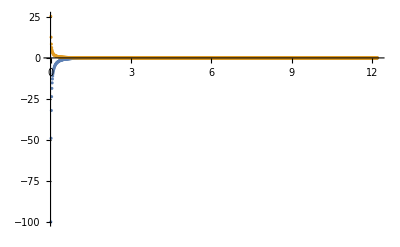

```mathematica
wlist=Table[ii,{ii,$interval,$finiteSize,$interval}];
num=Table[numList[[ii]] ,{ii,Length@wlist}];
wfFRe=Transpose[{wlist,Re/@num}];
wfFIm=Transpose[{wlist,Im/@num}];
ListPlot[{wfFRe,wfFIm},PlotRange->All]
```

## PlotMM

```mathematica
numList=Table[NIntegrate[amp10MM/.ω->ii,{zv,0,∞}],{ii,$interval,$finiteSize,$interval}];
```

```mathematica
(*Monitor[wf1list1=Table[ampNumUnReg=amp1Reg/.ω->ii;NIntegrate[ampNumUnReg,{zv,0,7},{zb,-π*7,+π*7},Method->"LocalAdaptive"],{ii,0.2,0.4,0.1}];,ii]*)
```

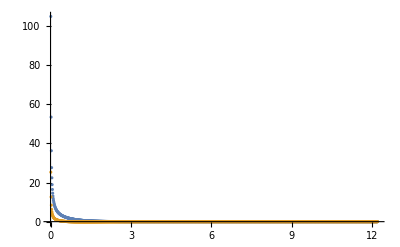

```mathematica
num=Table[(*time domain*)numList[[ii]] ,{ii,Length@wlist}];
wfFmmRe=Transpose[{wlist,Re/@num}];
wfFmmIm=Transpose[{wlist,Im/@num}];
ListPlot[{wfFmmRe,wfFmmIm},PlotRange->All]
```

## time domain

```mathematica
wf1PP=((Part[#,2]&/@ wfFRe)+I (Part[#,2]&/@ wfFRe));
wf1MM=((Part[#,2]&/@ wfFmmRe)+I (Part[#,2]&/@ wfFmmIm));
```

```mathematica
(*wf1PP=wf1PP[[minomega;;-1]];
wf1MM=wf1MM[[minomega;;-1]];*)
```

```mathematica
omegas
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.,2.01,2.02,2.03,2.04,2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,2.21,2.22,2.23,2.24,2.25,2.26,2.27,2.28,2.29,2.3,2.31,2.32,2.33,2.34,2.35,2.36,2.37,2.38,2.39,2.4,2.41,2.42,2.43,2.44,2.45,2.46,2.47,2.48,2.49,2.5,2.51,2.52,2.53,2.54,2.55,2.56,2.57,2.58,2.59,2.6,2.61,2.62,2.63,2.64,2.65,2.66,2.67,2.68,2.69,2.7,2.71,2.72,2.73,2.74,2.75,2.76,2.77,2.78,2.79,2.8,2.81,2.82,2.83,2.84,2.85,2.86,2.87,2.88,2.89,2.9,2.91,2.92,2.93,2.94,2.95,2.96,2.97,2.98,2.99,3.,3.01,3.02,3.03,3.04,3.05,3.06,3.07,3.08,3.09,3.1,3.11,3.12,3.13,3.14,3.15,3.16,3.17,3.18,3.19,3.2,3.21,3.22,3.23,3.24,3.25,3.26,3.27,3.28,3.29,3.3,3.31,3.32,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.41,3.42,3.43,3.44,3.45,3.46,3.47,3.48,3.49,3.5,3.51,3.52,3.53,3.54,3.55,3.56,3.57,3.58,3.59,3.6,3.61,3.62,3.63,3.64,3.65,3.66,3.67,3.68,3.69,3.7,3.71,3.72,3.73,3.74,3.75,3.76,3.77,3.78,3.79,3.8,3.81,3.82,3.83,3.84,3.85,3.86,3.87,3.88,3.89,3.9,3.91,3.92,3.93,3.94,3.95,3.96,3.97,3.98,3.99,4.,4.01,4.02,4.03,4.04,4.05,4.06,4.07,4.08,4.09,4.1,4.11,4.12,4.13,4.14,4.15,4.16,4.17,4.18,4.19,4.2,4.21,4.22,4.23,4.24,4.25,4.26,4.27,4.28,4.29,4.3,4.31,4.32,4.33,4.34,4.35,4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,4.5,4.51,4.52,4.53,4.54,4.55,4.56,4.57,4.58,4.59,4.6,4.61,4.62,4.63,4.64,4.65,4.66,4.67,4.68,4.69,4.7,4.71,4.72,4.73,4.74,4.75,4.76,4.77,4.78,4.79,4.8,4.81,4.82,4.83,4.84,4.85,4.86,4.87,4.88,4.89,4.9,4.91,4.92,4.93,4.94,4.95,4.96,4.97,4.98,4.99,5.,5.01,5.02,5.03,5.04,5.05,5.06,5.07,5.08,5.09,5.1,5.11,5.12,5.13,5.14,5.15,5.16,5.17,5.18,5.19,5.2,5.21,5.22,5.23,5.24,5.25,5.26,5.27,5.28,5.29,5.3,5.31,5.32,5.33,5.34,5.35,5.36,5.37,5.38,5.39,5.4,5.41,5.42,5.43,5.44,5.45,5.46,5.47,5.48,5.49,5.5,5.51,5.52,5.53,5.54,5.55,5.56,5.57,5.58,5.59,5.6,5.61,5.62,5.63,5.64,5.65,5.66,5.67,5.68,5.69,5.7,5.71,5.72,5.73,5.74,5.75,5.76,5.77,5.78,5.79,5.8,5.81,5.82,5.83,5.84,5.85,5.86,5.87,5.88,5.89,5.9,5.91,5.92,5.93,5.94,5.95,5.96,5.97,5.98,5.99,6.,6.01,6.02,6.03,6.04,6.05,6.06,6.07,6.08,6.09,6.1,6.11,6.12,6.13,6.14,6.15,6.16,6.17,6.18,6.19,6.2,6.21,6.22,6.23,6.24,6.25,6.26,6.27,6.28,6.29,6.3,6.31,6.32,6.33,6.34,6.35,6.36,6.37,6.38,6.39,6.4,6.41,6.42,6.43,6.44,6.45,6.46,6.47,6.48,6.49,6.5,6.51,6.52,6.53,6.54,6.55,6.56,6.57,6.58,6.59,6.6,6.61,6.62,6.63,6.64,6.65,6.66,6.67,6.68,6.69,6.7,6.71,6.72,6.73,6.74,6.75,6.76,6.77,6.78,6.79,6.8,6.81,6.82,6.83,6.84,6.85,6.86,6.87,6.88,6.89,6.9,6.91,6.92,6.93,6.94,6.95,6.96,6.97,6.98,6.99,7.,7.01,7.02,7.03,7.04,7.05,7.06,7.07,7.08,7.09,7.1,7.11,7.12,7.13,7.14,7.15,7.16,7.17,7.18,7.19,7.2,7.21,7.22,7.23,7.24,7.25,7.26,7.27,7.28,7.29,7.3,7.31,7.32,7.33,7.34,7.35,7.36,7.37,7.38,7.39,7.4,7.41,7.42,7.43,7.44,7.45,7.46,7.47,7.48,7.49,7.5,7.51,7.52,7.53,7.54,7.55,7.56,7.57,7.58,7.59,7.6,7.61,7.62,7.63,7.64,7.65,7.66,7.67,7.68,7.69,7.7,7.71,7.72,7.73,7.74,7.75,7.76,7.77,7.78,7.79,7.8,7.81,7.82,7.83,7.84,7.85,7.86,7.87,7.88,7.89,7.9,7.91,7.92,7.93,7.94,7.95,7.96,7.97,7.98,7.99,8.,8.01,8.02,8.03,8.04,8.05,8.06,8.07,8.08,8.09,8.1,8.11,8.12,8.13,8.14,8.15,8.16,8.17,8.18,8.19,8.2,8.21,8.22,8.23,8.24,8.25,8.26,8.27,8.28,8.29,8.3,8.31,8.32,8.33,8.34,8.35,8.36,8.37,8.38,8.39,8.4,8.41,8.42,8.43,8.44,8.45,8.46,8.47,8.48,8.49,8.5,8.51,8.52,8.53,8.54,8.55,8.56,8.57,8.58,8.59,8.6,8.61,8.62,8.63,8.64,8.65,8.66,8.67,8.68,8.69,8.7,8.71,8.72,8.73,8.74,8.75,8.76,8.77,8.78,8.79,8.8,8.81,8.82,8.83,8.84,8.85,8.86,8.87,8.88,8.89,8.9,8.91,8.92,8.93,8.94,8.95,8.96,8.97,8.98,8.99,9.,9.01,9.02,9.03,9.04,9.05,9.06,9.07,9.08,9.09,9.1,9.11,9.12,9.13,9.14,9.15,9.16,9.17,9.18,9.19,9.2,9.21,9.22,9.23,9.24,9.25,9.26,9.27,9.28,9.29,9.3,9.31,9.32,9.33,9.34,9.35,9.36,9.37,9.38,9.39,9.4,9.41,9.42,9.43,9.44,9.45,9.46,9.47,9.48,9.49,9.5,9.51,9.52,9.53,9.54,9.55,9.56,9.57,9.58,9.59,9.6,9.61,9.62,9.63,9.64,9.65,9.66,9.67,9.68,9.69,9.7,9.71,9.72,9.73,9.74,9.75,9.76,9.77,9.78,9.79,9.8,9.81,9.82,9.83,9.84,9.85,9.86,9.87,9.88,9.89,9.9,9.91,9.92,9.93,9.94,9.95,9.96,9.97,9.98,9.99,10.,10.01,10.02,10.03,10.04,10.05,10.06,10.07,10.08,10.09,10.1,10.11,10.12,10.13,10.14,10.15,10.16,10.17,10.18,10.19,10.2,10.21,10.22,10.23,10.24,10.25,10.26,10.27,10.28,10.29,10.3,10.31,10.32,10.33,10.34,10.35,10.36,10.37,10.38,10.39,10.4,10.41,10.42,10.43,10.44,10.45,10.46,10.47,10.48,10.49,10.5,10.51,10.52,10.53,10.54,10.55,10.56,10.57,10.58,10.59,10.6,10.61,10.62,10.63,10.64,10.65,10.66,10.67,10.68,10.69,10.7,10.71,10.72,10.73,10.74,10.75,10.76,10.77,10.78,10.79,10.8,10.81,10.82,10.83,10.84,10.85,10.86,10.87,10.88,10.89,10.9,10.91,10.92,10.93,10.94,10.95,10.96,10.97,10.98,10.99,11.,11.01,11.02,11.03,11.04,11.05,11.06,11.07,11.08,11.09,11.1,11.11,11.12,11.13,11.14,11.15,11.16,11.17,11.18,11.19,11.2,11.21,11.22,11.23,11.24,11.25,11.26,11.27,11.28,11.29,11.3,11.31,11.32,11.33,11.34,11.35,11.36,11.37,11.38,11.39,11.4,11.41,11.42,11.43,11.44,11.45,11.46,11.47,11.48,11.49,11.5,11.51,11.52,11.53,11.54,11.55,11.56,11.57,11.58,11.59,11.6,11.61,11.62,11.63,11.64,11.65,11.66,11.67,11.68,11.69,11.7,11.71,11.72,11.73,11.74,11.75,11.76,11.77,11.78,11.79,11.8,11.81,11.82,11.83,11.84,11.85,11.86,11.87,11.88,11.89,11.9,11.91,11.92,11.93,11.94,11.95,11.96,11.97,11.98,11.99,12.,12.01,12.02,12.03,12.04,12.05,12.06,12.07,12.08,12.09,12.1,12.11,12.12,12.13,12.14,12.15,12.16,12.17,12.18,12.19,12.2}

```mathematica
omegas=wlist;
```

```mathematica
exp1=Table[Exp[-I ω t]/.ω->i,{i,omegas}];
exp2=Table[Exp[I ω t]/.ω->i,{i,omegas}];
```

```mathematica
0.1*(exp1*wf1PP+exp2*Conjugate[wf1MM])//Total
```

0.1 ((-256.969-256.969 ⅈ) ⅇ^((0.-0.1 ⅈ) t)+(203.066-100.561 ⅈ) ⅇ^((0.+0.1 ⅈ) t))+600+0.1 ((4.09791×10^-17+4.09791×10^-17 ⅈ) ⅇ^((0.-60.2 ⅈ) t)-(1.60889×10^-16+5.97905×10^-16 ⅈ) ⅇ^1)
 |  |  |  |

```mathematica
Total[ 0.005*(exp1*wf1PP+exp2*wf1PP)]/.t->0
```

-4.18671-4.18671 ⅈ

```mathematica
wft=Total[ 0.005*(exp1*wf1PP+exp2*wf1PP)];
```

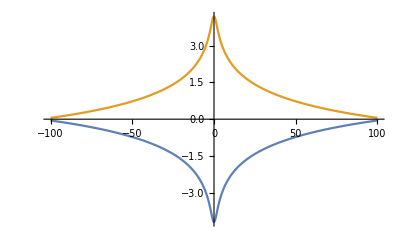

```mathematica
wft=Total[ 0.005*(exp1*wf1PP+exp2*wf1PP)];
Plot[{Re[wft],-Im[wft]},{t,-100,100},PlotRange->All]
```

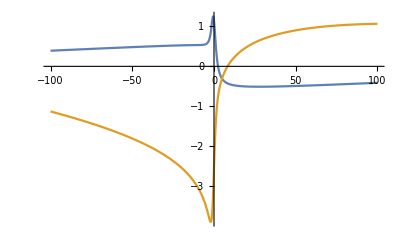

```mathematica
wft=Total[ 0.005*(exp1*wf1PP+exp2*Conjugate[wf1MM])];
Plot[{Re[wft],Im[wft]},{t,-100,100},PlotRange->All]
```

```mathematica
(*ListPlot[Transpose[{Table[x,{x,-$finiteSize,$finiteSize,$interval}],%}]]*)
```

```mathematica
wft
```

0.1 ((-1.99333-1.99333 ⅈ) ⅇ^((0.-0.2 ⅈ) t)-(1.98392+3.75034 ⅈ) ⅇ^((0.+0.2 ⅈ) t))+0.1 ((-3.85147-3.85147 ⅈ) ⅇ^((0.-0.4 ⅈ) t)-(3.75343+6.67237 ⅈ) ⅇ^((0.+0.4 ⅈ) t))+0.1 ((-5.48956-5.48956 ⅈ) ⅇ^((0.-0.6 ⅈ) t)-(5.13644+9.10035 ⅈ) ⅇ^((0.+0.6 ⅈ) t))+0.1 ((-6.85907-6.85907 ⅈ) ⅇ^((0.-0.8 ⅈ) t)-(6.03474+11.1042 ⅈ) ⅇ^((0.+0.8 ⅈ) t))+0.1 ((-7.93769-7.93769 ⅈ) ⅇ^((0.-1. ⅈ) t)-(6.42092+12.6916 ⅈ) ⅇ^((0.+1. ⅈ) t))+0.1 ((-8.72243-8.72243 ⅈ) ⅇ^((0.-1.2 ⅈ) t)-(6.32372+13.8552 ⅈ) ⅇ^((0.+1.2 ⅈ) t))+0.1 ((-9.22426-9.22426 ⅈ) ⅇ^((0.-1.4 ⅈ) t)-(5.8108+14.5913 ⅈ) ⅇ^((0.+1.4 ⅈ) t))+0.1 ((-9.46391-9.46391 ⅈ) ⅇ^((0.-1.6 ⅈ) t)-(4.97273+14.9078 ⅈ) ⅇ^((0.+1.6 ⅈ) t))+0.1 ((-9.46849-9.46849 ⅈ) ⅇ^((0.-1.8 ⅈ) t)-(3.90959+14.8271 ⅈ) ⅇ^((0.+1.8 ⅈ) t))+0.1 ((-9.26893-9.26893 ⅈ) ⅇ^((0.-2. ⅈ) t)-(2.72056+14.3851 ⅈ) ⅇ^((0.+2. ⅈ) t))+0.1 ((-8.89785-8.89785 ⅈ) ⅇ^((0.-2.2 ⅈ) t)-(1.49654+13.629 ⅈ) ⅇ^((0.+2.2 ⅈ) t))+0.1 ((-8.3881-8.3881 ⅈ) ⅇ^((0.-2.4 ⅈ) t)-(0.315324+12.614 ⅈ) ⅇ^((0.+2.4 ⅈ) t))+0.1 ((-7.77151-7.77151 ⅈ) ⅇ^((0.-2.6 ⅈ) t)+(0.760949-11.4 ⅈ) ⅇ^((0.+2.6 ⅈ) t))+0.1 ((-7.07806-7.07806 ⅈ) ⅇ^((0.-2.8 ⅈ) t)+(1.6867-10.048 ⅈ) ⅇ^((0.+2.8 ⅈ) t))+0.1 ((-6.33528-6.33528 ⅈ) ⅇ^((0.-3. ⅈ) t)+(2.43244-8.61705 ⅈ) ⅇ^((0.+3. ⅈ) t))+0.1 ((-5.56786-5.56786 ⅈ) ⅇ^((0.-3.2 ⅈ) t)+(2.98341-7.16232 ⅈ) ⅇ^((0.+3.2 ⅈ) t))+0.1 ((-4.79741-4.79741 ⅈ) ⅇ^((0.-3.4 ⅈ) t)+(3.33763-5.73269 ⅈ) ⅇ^((0.+3.4 ⅈ) t))+0.1 ((-4.04238-4.04238 ⅈ) ⅇ^((0.-3.6 ⅈ) t)+(3.50362-4.3698 ⅈ) ⅇ^((0.+3.6 ⅈ) t))+0.1 ((-3.31805-3.31805 ⅈ) ⅇ^((0.-3.8 ⅈ) t)+(3.49802-3.10728 ⅈ) ⅇ^((0.+3.8 ⅈ) t))+0.1 ((-2.63665-2.63665 ⅈ) ⅇ^((0.-4. ⅈ) t)+(3.34325-1.97051 ⅈ) ⅇ^((0.+4. ⅈ) t))+0.1 ((-2.00749-2.00749 ⅈ) ⅇ^((0.-4.2 ⅈ) t)+(3.06536-0.976841 ⅈ) ⅇ^((0.+4.2 ⅈ) t))+0.1 ((-1.43721-1.43721 ⅈ) ⅇ^((0.-4.4 ⅈ) t)+(2.69212-0.136099 ⅈ) ⅇ^((0.+4.4 ⅈ) t))+0.1 ((-0.930002-0.930002 ⅈ) ⅇ^((0.-4.6 ⅈ) t)+(2.2514+0.548647 ⅈ) ⅇ^((0.+4.6 ⅈ) t))+0.1 ((-0.487871-0.487871 ⅈ) ⅇ^((0.-4.8 ⅈ) t)+(1.76983+1.08018 ⅈ) ⅇ^((0.+4.8 ⅈ) t))+0.1 ((-0.110937-0.110937 ⅈ) ⅇ^((0.-5. ⅈ) t)+(1.27185+1.46611 ⅈ) ⅇ^((0.+5. ⅈ) t))+0.1 ((0.202288+0.202288 ⅈ) ⅇ^((0.-5.2 ⅈ) t)+(0.77895+1.71787 ⅈ) ⅇ^((0.+5.2 ⅈ) t))+0.1 ((0.454619+0.454619 ⅈ) ⅇ^((0.-5.4 ⅈ) t)+(0.309239+1.84964 ⅈ) ⅇ^((0.+5.4 ⅈ) t))+0.1 ((0.64992+0.64992 ⅈ) ⅇ^((0.-5.6 ⅈ) t)-(0.122755-1.87745 ⅈ) ⅇ^((0.+5.6 ⅈ) t))+0.1 ((0.792852+0.792852 ⅈ) ⅇ^((0.-5.8 ⅈ) t)-(0.506114-1.81829 ⅈ) ⅇ^((0.+5.8 ⅈ) t))+0.1 ((0.888625+0.888625 ⅈ) ⅇ^((0.-6. ⅈ) t)-(0.833388-1.68933 ⅈ) ⅇ^((0.+6. ⅈ) t))+0.1 ((0.942792+0.942792 ⅈ) ⅇ^((0.-6.2 ⅈ) t)-(1.10033-1.5073 ⅈ) ⅇ^((0.+6.2 ⅈ) t))+0.1 ((0.961049+0.961049 ⅈ) ⅇ^((0.-6.4 ⅈ) t)-(1.30556-1.28799 ⅈ) ⅇ^((0.+6.4 ⅈ) t))+0.1 ((0.949073+0.949073 ⅈ) ⅇ^((0.-6.6 ⅈ) t)-(1.45013-1.04583 ⅈ) ⅇ^((0.+6.6 ⅈ) t))+0.1 ((0.912378+0.912378 ⅈ) ⅇ^((0.-6.8 ⅈ) t)-(1.53714-0.793618 ⅈ) ⅇ^((0.+6.8 ⅈ) t))+0.1 ((0.856203+0.856203 ⅈ) ⅇ^((0.-7. ⅈ) t)-(1.57127-0.542346 ⅈ) ⅇ^((0.+7. ⅈ) t))+0.1 ((0.785422+0.785422 ⅈ) ⅇ^((0.-7.2 ⅈ) t)-(1.55834-0.301133 ⅈ) ⅇ^((0.+7.2 ⅈ) t))+0.1 ((0.704476+0.704476 ⅈ) ⅇ^((0.-7.4 ⅈ) t)-(1.50496-0.0772164 ⅈ) ⅇ^((0.+7.4 ⅈ) t))+0.1 ((0.617328+0.617328 ⅈ) ⅇ^((0.-7.6 ⅈ) t)-(1.41814+0.123978 ⅈ) ⅇ^((0.+7.6 ⅈ) t))+0.1 ((0.527439+0.527439 ⅈ) ⅇ^((0.-7.8 ⅈ) t)-(1.30497+0.298716 ⅈ) ⅇ^((0.+7.8 ⅈ) t))+0.1 ((0.437759+0.437759 ⅈ) ⅇ^((0.-8. ⅈ) t)-(1.17239+0.444801 ⅈ) ⅇ^((0.+8. ⅈ) t))+0.1 ((0.350733+0.350733 ⅈ) ⅇ^((0.-8.2 ⅈ) t)-(1.02694+0.561386 ⅈ) ⅇ^((0.+8.2 ⅈ) t))+0.1 ((0.268321+0.268321 ⅈ) ⅇ^((0.-8.4 ⅈ) t)-(0.87463+0.648773 ⅈ) ⅇ^((0.+8.4 ⅈ) t))+0.1 ((0.192024+0.192024 ⅈ) ⅇ^((0.-8.6 ⅈ) t)-(0.720797+0.708215 ⅈ) ⅇ^((0.+8.6 ⅈ) t))+0.1 ((0.122923+0.122923 ⅈ) ⅇ^((0.-8.8 ⅈ) t)-(0.570038+0.74171 ⅈ) ⅇ^((0.+8.8 ⅈ) t))+0.1 ((0.0617167+0.0617167 ⅈ) ⅇ^((0.-9. ⅈ) t)-(0.426177+0.751806 ⅈ) ⅇ^((0.+9. ⅈ) t))+0.1 ((0.00877131+0.00877131 ⅈ) ⅇ^((0.-9.2 ⅈ) t)-(0.292259+0.74143 ⅈ) ⅇ^((0.+9.2 ⅈ) t))+0.1 ((-0.0358377-0.0358377 ⅈ) ⅇ^((0.-9.4 ⅈ) t)-(0.170572+0.713722 ⅈ) ⅇ^((0.+9.4 ⅈ) t))+0.1 ((-0.0722766-0.0722766 ⅈ) ⅇ^((0.-9.6 ⅈ) t)-(0.062695+0.671895 ⅈ) ⅇ^((0.+9.6 ⅈ) t))+0.1 ((-0.100909-0.100909 ⅈ) ⅇ^((0.-9.8 ⅈ) t)+(0.0304427-0.619121 ⅈ) ⅇ^((0.+9.8 ⅈ) t))+0.1 ((-0.122251-0.122251 ⅈ) ⅇ^((0.-10. ⅈ) t)+(0.108488-0.558429 ⅈ) ⅇ^((0.+10. ⅈ) t))+0.1 ((-0.136934-0.136934 ⅈ) ⅇ^((0.-10.2 ⅈ) t)+(0.171584-0.492634 ⅈ) ⅇ^((0.+10.2 ⅈ) t))+0.1 ((-0.145665-0.145665 ⅈ) ⅇ^((0.-10.4 ⅈ) t)+(0.220288-0.424276 ⅈ) ⅇ^((0.+10.4 ⅈ) t))+0.1 ((-0.149195-0.149195 ⅈ) ⅇ^((0.-10.6 ⅈ) t)+(0.255488-0.355588 ⅈ) ⅇ^((0.+10.6 ⅈ) t))+0.1 ((-0.148293-0.148293 ⅈ) ⅇ^((0.-10.8 ⅈ) t)+(0.278322-0.288472 ⅈ) ⅇ^((0.+10.8 ⅈ) t))+0.1 ((-0.143719-0.143719 ⅈ) ⅇ^((0.-11. ⅈ) t)+(0.290106-0.224495 ⅈ) ⅇ^((0.+11. ⅈ) t))+0.1 ((-0.136204-0.136204 ⅈ) ⅇ^((0.-11.2 ⅈ) t)+(0.292266-0.16489 ⅈ) ⅇ^((0.+11.2 ⅈ) t))+0.1 ((-0.12644-0.12644 ⅈ) ⅇ^((0.-11.4 ⅈ) t)+(0.286273-0.110576 ⅈ) ⅇ^((0.+11.4 ⅈ) t))+0.1 ((-0.115059-0.115059 ⅈ) ⅇ^((0.-11.6 ⅈ) t)+(0.273598-0.0621789 ⅈ) ⅇ^((0.+11.6 ⅈ) t))+0.1 ((-0.102635-0.102635 ⅈ) ⅇ^((0.-11.8 ⅈ) t)+(0.255665-0.0200586 ⅈ) ⅇ^((0.+11.8 ⅈ) t))+0.1 ((-0.0896706-0.0896706 ⅈ) ⅇ^((0.-12. ⅈ) t)+(0.233817+0.0156578 ⅈ) ⅇ^((0.+12. ⅈ) t))+0.1 ((-0.0765989-0.0765989 ⅈ) ⅇ^((0.-12.2 ⅈ) t)+(0.209291+0.0450429 ⅈ) ⅇ^((0.+12.2 ⅈ) t))

{{-5.,0.68091},{-4.9,0.759051},{-4.8,0.793584},{-4.7,0.8006},{-4.6,0.840121},{-4.5,0.936498},{-4.4,1.04386},{-4.3,1.10617},{-4.2,1.13444},{-4.1,1.19594},{-4.,1.32563},{-3.9,1.47705},{-3.8,1.58271},{-3.7,1.64725},{-3.6,1.7468},{-3.5,1.92956},{-3.4,2.14835},{-3.3,2.32102},{-3.2,2.44383},{-3.1,2.6042},{-3.,2.86695},{-2.9,3.18263},{-2.8,3.44761},{-2.7,3.6452},{-2.6,3.87621},{-2.5,4.22443},{-2.4,4.62927},{-2.3,4.94615},{-2.2,5.12882},{-2.1,5.28519},{-2.,5.50634},{-1.9,5.6806},{-1.8,5.55916},{-1.7,5.01757},{-1.6,4.1635},{-1.5,3.11229},{-1.4,1.74206},{-1.3,-0.100104},{-1.2,-1.98344},{-1.1,-2.58686},{-1.,-0.362387},{-0.9,5.11967},{-0.8,12.3451},{-0.7,18.5239},{-0.6,21.3937},{-0.5,20.6522},{-0.4,17.7926},{-0.3,14.6011},{-0.2,11.7743},{-0.1,8.82685},{0.,5.06577},{0.1,0.424648},{0.2,-4.65083},{0.3,-9.88116},{0.4,-15.4137},{0.5,-21.2954},{0.6,-26.8109},{0.7,-30.5651},{0.8,-31.38},{0.9,-29.1778},{1.,-25.0228},{1.1,-20.3446},{1.2,-16.1055},{1.3,-12.5716},{1.4,-9.64918},{1.5,-7.26232},{1.6,-5.41541},{1.7,-4.05061},{1.8,-3.00129},{1.9,-2.11723},{2.,-1.37593},{2.1,-0.829549},{2.2,-0.471657},{2.3,-0.205631},{2.4,0.0545349},{2.5,0.297453},{2.6,0.456975},{2.7,0.519913},{2.8,0.553302},{2.9,0.621303},{3.,0.708703},{3.1,0.751734},{3.2,0.729825},{3.3,0.694513},{3.4,0.701122},{3.5,0.738236},{3.6,0.747897},{3.7,0.705675},{3.8,0.652623},{3.9,0.639414},{4.,0.660037},{4.1,0.66269},{4.2,0.620325},{4.3,0.5657},{4.4,0.546286},{4.5,0.561466},{4.6,0.565284},{4.7,0.528729},{4.8,0.477466},{4.9,0.456266},{5.,0.469452}}

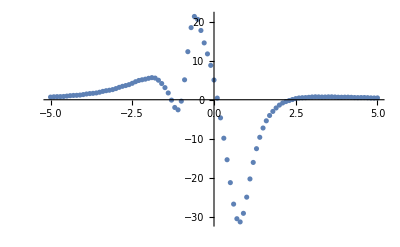

```mathematica
Table[{ii,wft/.t->ii//Re},{ii,-5,5,0.1}]
ListPlot[%,PlotRange->All]
```

{{-5.,1.53452},{-4.9,1.6439},{-4.8,1.7702},{-4.7,1.82395},{-4.6,1.81498},{-4.5,1.84404},{-4.4,1.97005},{-4.3,2.12778},{-4.2,2.21084},{-4.1,2.21543},{-4.,2.25159},{-3.9,2.39921},{-3.8,2.59687},{-3.7,2.71783},{-3.6,2.74053},{-3.5,2.78538},{-3.4,2.95853},{-3.3,3.20405},{-3.2,3.36899},{-3.1,3.40727},{-3.,3.45118},{-2.9,3.64051},{-2.8,3.92544},{-2.7,4.11454},{-2.6,4.1234},{-2.5,4.09557},{-2.4,4.2117},{-2.3,4.419},{-2.2,4.45046},{-2.1,4.13892},{-2.,3.61236},{-1.9,3.06443},{-1.8,2.35015},{-1.7,0.942953},{-1.6,-1.64651},{-1.5,-5.55527},{-1.4,-10.8979},{-1.3,-18.4189},{-1.2,-29.4387},{-1.1,-44.572},{-1.,-62.1367},{-0.9,-77.988},{-0.8,-87.5414},{-0.7,-88.6847},{-0.6,-83.167},{-0.5,-75.18},{-0.4,-68.262},{-0.3,-63.0739},{-0.2,-57.697},{-0.1,-49.834},{0.,-38.8403},{0.1,-26.0408},{0.2,-13.5081},{0.3,-2.63622},{0.4,6.39133},{0.5,14.1774},{0.6,21.3661},{0.7,28.143},{0.8,34.1351},{0.9,38.6225},{1.,40.9438},{1.1,40.9215},{1.2,39.0373},{1.3,36.1842},{1.4,33.153},{1.5,30.2784},{1.6,27.515},{1.7,24.7874},{1.8,22.2082},{1.9,19.9693},{2.,18.1093},{2.1,16.4738},{2.2,14.9079},{2.3,13.4275},{2.4,12.1596},{2.5,11.1484},{2.6,10.282},{2.7,9.42516},{2.8,8.57499},{2.9,7.83943},{3.,7.27741},{3.1,6.81316},{3.2,6.3302},{3.3,5.81403},{3.4,5.35697},{3.5,5.02604},{3.6,4.77098},{3.7,4.48938},{3.8,4.15698},{3.9,3.85138},{4.,3.64302},{4.1,3.50062},{4.2,3.33317},{4.3,3.10829},{4.4,2.88985},{4.5,2.74908},{4.6,2.6696},{4.7,2.57041},{4.8,2.41257},{4.9,2.2474},{5.,2.14522}}

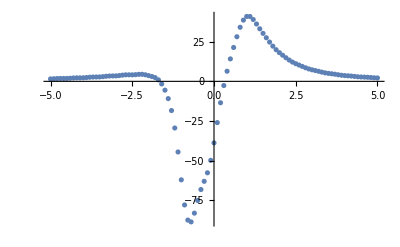

```mathematica
Table[{ii,wft/.t->ii//Im},{ii,-5,5,0.1}]
ListPlot[%,PlotRange->All]
```